```mathematica
ClearAll["Global`*"];
(*Analytical simulation of motion of projectile*)
x0=0;y0=100;
v0=60;θ=45 Degree;
g=-9.81;
P[s_]={x0+v0 Cos[θ] s ,y0+v0 Sin[θ] s+g s^2/2}//N;
tpeak=s/.(Solve[D[P[s][[2]],s]==0,s])[[1]];
tground=s/.(Solve[P[s][[2]]==0,s])[[2]];
```

```mathematica
Manipulate[
axis=Graphics[{
{White,Arrowheads[0.02],Arrow[{{0,0},{1.1 P[tground][[1]],0}}]},
{White,Arrowheads[0.02],Arrow[{{0,0},{0,1.1 P[tpeak][[2]]}}]}
}];
axis1=Graphics[{
{Green,Thickness->Thin,Line[{{x0,y0},{x0+20,y0}}]},
{Green,Arrowheads[0.012],Arrow[{{x0,y0},{x0+20Cos[θ],y0+20 Sin[θ]}}]}
}];
max=Graphics[{
White,Dashed,Line[{{P[tpeak][[1]],0},{P[tpeak][[1]],P[tpeak][[2]]}}]
}];
Show[{
axis,
axis1,
max,
ParametricPlot[P[t0],{t0,0,t}],
Graphics[{Red,PointSize[0.01],Point[P[t]]}]},
PlotRange->{{-5,500},{-5,300}},
Boxed->False,ImageSize->Large,Background->Black,Lighting->{{"Ambient", LightBlue}},
LightingAngle->{0,Pi/12},AspectRatio->1],
{t,0.01,tground}(*,{{po,{0,10}},Locator}*)
]
```

```mathematica
(*Comparsion between analytical solution and solving Runge kutta method *)
(*First solution in x direction *)
t0=0;
tf=10;
n=100;
t=Table[j,{j,1,n+1}];
x1=Table[j,{j,1,n+1}];
x2=Table[j,{j,1,n+1}];
(* Initial conditions *)
t[[1]]=t0;
x1[[1]]=x0;
x2[[1]]=v0  Cos[θ]//N;
f1[t_,x1_,x2_]:=x2
f2[t_,x1_,x2_]:=0;
h=(tf-t0)/n;
For[i=1,i<n+1,i++,
{
k1=f1[t[[i]],x1[[i]],x2[[i]]];
m1=f2[t[[i]],x1[[i]],x2[[i]]];
k2=f1[t[[i]]+h/2,x1[[i]]+h k1/2,x2[[i]]+h m1/2];
m2=f2[t[[i]]+h/2,x1[[i]]+h k1/2,x2[[i]]+h m1/2];
k3=f1[t[[i]]+h/2,x1[[i]]+h k2/2,x2[[i]]+h m2/2];
m3=f2[t[[i]]+h/2,x1[[i]]+h k2/2,x2[[i]]+h m2/2];
k4=f1[t[[i]]+h,x1[[i]]+h k3,x2[[i]]+h m3];
m4=f2[t[[i]]+h,x1[[i]]+h k3,x2[[i]]+h m3];
(*Find iteration solution *)
t[[i+1]]=t[[i]]+h;
x1[[i+1]]=x1[[i]]+h/6(k1+2 k2+2 k3+k4);
x2[[i+1]]=x2[[i]]+h/6(m1+2 m2+2 m3+m4);
}]
(*Solution in y direction *)
y1=Table[j,{j,1,n+1}];
y2=Table[j,{j,1,n+1}];
(* Initial conditions *)
y1[[1]]=y0;
y2[[1]]=v0  Sin[θ]//N;
f1[t_,y1_,y2_]:=y2
f2[t_,y1_,y2_]:=g;
For[i=1,i<n+1,i++,
{
k1=f1[t[[i]],y1[[i]],y2[[i]]];
m1=f2[t[[i]],y1[[i]],y2[[i]]];
k2=f1[t[[i]]+h/2,y1[[i]]+h k1/2,y2[[i]]+h m1/2];
m2=f2[t[[i]]+h/2,y1[[i]]+h k1/2,y2[[i]]+h m1/2];
k3=f1[t[[i]]+h/2,y1[[i]]+h k2/2,y2[[i]]+h m2/2];
m3=f2[t[[i]]+h/2,y1[[i]]+h k2/2,y2[[i]]+h m2/2];
k4=f1[t[[i]]+h,y1[[i]]+h k3,y2[[i]]+h m3];
m4=f2[t[[i]]+h,y1[[i]]+h k3,y2[[i]]+h m3];
(*Find iteration solution *)
t[[i+1]]=t[[i]]+h;
y1[[i+1]]=y1[[i]]+h/6(k1+2k2+2k3+k4);
y2[[i+1]]=y2[[i]]+h/6(m1+2m2+2m3+m4);
}]
```

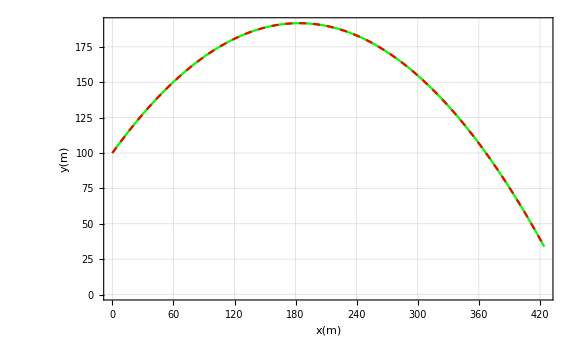

```mathematica
data=Table[{x1[[j]],y1[[j]]},{j,1,n+1}];
fig1=ListLinePlot[data,Frame-> True,PlotRange->All,PlotStyle->Green,
FrameLabel->{"x(m)","y(m)"},GridLines->None];
fig2=ParametricPlot[{P[t][[1]],P[t][[2]]},{t,0,tf},PlotStyle->{Dashed,Red}];
Show[{fig1,fig2},ImageSize->Large,PlotTheme->"Scientific",GridLines->Automatic,
GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}}]
```

```mathematica
error[i_]:=(P[i*h]-{x1[[i+1]],y1[[i+1]]})/P[i*h]*100;   (*% *)
```

```mathematica
errordata=Transpose[Table[error[i],{i,1,n}]];
```

```mathematica
maxerror={Max[errordata[[1]]],Max[errordata[[2]]]}
```

{1.64059×10^-13,1.36788×10^-12}